```mathematica
sf=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-a-n.wdx"];
ft2=Query[2,1]@sf;
```

```mathematica
pft2=Interpolation[Flatten[ft2,1]];
```

```mathematica
pft2[0.5,-1]
```

2.29182

```mathematica
Hq1=(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*Nv*β^(a-1)*(1-β)^b1*(1+c*β^d)/(1-t/λ1^2);
Hqa=(Hq1/.{α->(x-β)/ξ})/ξ;
Hqan=Hqa/.{a->0.7,b1->2,c->13.8,d->2,Nv->1/2,b0->2,λ1->0.79,t->-1,ξ->0.1,x->0.5};
Hqay[x_,t_]=Hqa/.{a->0.7,b1->2,c->13.8,d->2,Nv->1/2,b0->2,λ1->0.79,ξ->0.1/y,x->x/y};
```

```mathematica
Hft2q[x_,t_]=Hqay[x,t]*pft2[y,t]/y;
```

```mathematica
test[x_,t_]:=NIntegrate[Hft2q[x,t],{y,x,1},{β,(x-0.3)/(y-0.3),(x+0.3)/(y+0.3)},MinRecursion->10,MaxRecursion->20,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
```

```mathematica
test[0.5,-1]
```

2.986329439

```mathematica
2.9863294387995534918918059294810966523`10.(*0.5,-1*)
```

2.986329439

```mathematica
Hft2q[x,-1]
```

(1.80129 (1-β)^2 (1+13.8 β^2) (-100. y^2 (x/y-β)^2+(1-Abs[β])^2)^2 InterpolatingFunction[…][y,-1])/(β^0.3 (1-Abs[β])^5)

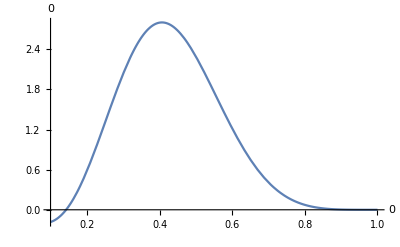

```mathematica
Plot[pft2[y,-1],{y,0.1,1},AxesLabel->{0,0}]
```

```mathematica
NIntegrate[pft2[y,-1],{y,0.1,1}]
```

0.933186

```mathematica
NIntegrate[Hqay[0.3]*pft2[y,-1]/y,{y,0.3,1},{β,(0.3-0.1)/(y-0.1),(0.3+0.1)/(y+0.1)},MinRecursion->10,MaxRecursion->20,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

NIntegrate::inumr: The integrand (Hqay[0.3] «1»)/y has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.03125},{0,0.03125}}.

NIntegrate[(Hqay[0.3] pft2[y,-1])/y,{y,0.3,1},{β,(0.3-0.1)/(y-0.1),(0.3+0.1)/(y+0.1)},MinRecursion→10,MaxRecursion→20,WorkingPrecision→10,AccuracyGoal→10,Method→{GlobalAdaptive,Method→ClenshawCurtisRule}]

```mathematica
Hqay[0.3]
```

Hqay[0.3]